## Limit Cycle and iPRC Calculations

```mathematica
f=√(a+b sx-c sy);
```

```mathematica
Simplify[Integrate[1/((1-Cos[x]+(1+Cos[x])f^2)*Pi),x]]
```

ArcTan[Tan[x/2]/f]/(f π)

Solving for x above results in the limit cycle equation

```mathematica
FullSimplify[Solve[ArcTan[Tan[x/2]/f]/(f π)==t,x]]
```

{{x→ConditionalExpression[2 (ArcTan[f Tan[f π t]]+π C[1]),((1+2 Re[f t]==0&&Im[f t]<0)||-π/2<π Re[f t]<π/2||(2 Re[f t]==1&&Im[f t]>0))&&C[1]∈Integers]}}

```mathematica
x(t)=2arctan(f tan(f π t)),
```

where f=√(a+b s_x-c s_y).

```mathematica
LC[t_]=2ArcTan[f Tan[f π (t+1/(2 f))]];
```

To solve for the iPRC, we recall that 1/(f(x_0(t)))=1/(x_0'(t))and simplify. The direct simplification using mathematica yields

```mathematica
Z[t_]=Simplify[1/D[LC[t],t]];
```

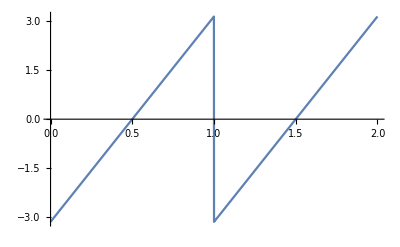

```mathematica
Plot[LC[t]/.sx->1/.sy->1/.a->.5/.b-> 7/.c->6.5,{t,0,2}]
```

```mathematica
Plot[Z[t]/.sx->1/.sy->1/.a->.5/.b-> 7/.c->6.5,{t,0,1}]
```

-Graphics-

To find the Beta functions, we require knowing the derivative of the limit cycle with respect to the first slow variable. First rescale time so that all the limit cycles are 2Pi periodic.

```mathematica
2arctan(f tan(f π (t+1/(2f))))=2arctan(f tan(f π t+π/2)))
```

```mathematica
FullSimplify[D[2ArcTan[Sqrt[a+b sx - c sy]Tan[π Sqrt[a+b sx - c sy]t+π/2]],sx]]
```

(b (-Cot[π √(a+b sx-c sy) t]/(√(a+b sx-c sy))+π t Csc[π √(a+b sx-c sy) t]^2))/(1+(a+b sx-c sy) Cot[π √(a+b sx-c sy) t]^2)

```mathematica
FullSimplify[D[2ArcTan[Sqrt[a+b sx - c sy]Tan[π Sqrt[a+b sx - c sy]t+π/2]],sy]]
```

(c (Cot[π √(a+b sx-c sy) t]/(√(a+b sx-c sy))-π t Csc[π √(a+b sx-c sy) t]^2))/(1+(a+b sx-c sy) Cot[π √(a+b sx-c sy) t]^2)

```mathematica
ff[t_]:=(b (-Cot[π √(a+b sx-c sy) t]/(√(a+b sx-c sy))+π t Csc[π √(a+b sx-c sy) t]^2))/(1+(a+b sx-c sy) Cot[π √(a+b sx-c sy) t]^2)/.a->.5/.b->7/.c->6.5
```

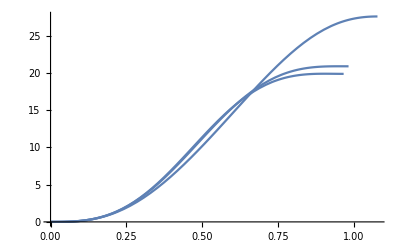

```mathematica
p1=Plot[ff[t]/.sx->1.005/.sy->1,{t,0,1/(√(a+b sx-c sy))/.a->.5/.b->7/.c->6.5/.sx->1.005/.sy->1},PlotRange->All];
p2=Plot[ff[t]/.sx->1.01/.sy->1,{t,0,1/(√(a+b sx-c sy))/.a->.5/.b->7/.c->6.5/.sx->1.01/.sy->1},PlotRange->All];
p3=Plot[ff[t]/.sx->.98/.sy->1,{t,0,1/(√(a+b sx-c sy))/.a->.5/.b->7/.c->6.5/.sx->.98/.sy->1},PlotRange->All];
Show[p1,p2,p3]
```

```mathematica
lc[t_]:=2ArcTan[Sqrt[a+b sx - c sy]Tan[π Sqrt[a+b sx - c sy]t+π/2]]/.a->.5/.b->7/.c->6.5;
```

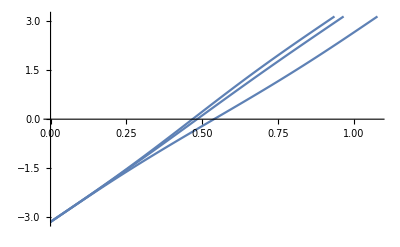

```mathematica
L1=Plot[lc[t]/.sx-> 1.02/.sy->1,{t,0,1/(√(a+b sx-c sy))/.a->.5/.b->7/.c->6.5/.sx->1.02/.sy->1},PlotRange->All];
L2=Plot[lc[t]/.sx->1.01/.sy->1,{t,0,1/(√(a+b sx-c sy))/.a->.5/.b->7/.c->6.5/.sx->1.01/.sy->1},PlotRange->All];
L3=Plot[lc[t]/.sx->.98/.sy->1,{t,0,1/(√(a+b sx-c sy))/.a->.5/.b->7/.c->6.5/.sx->.98/.sy->1},PlotRange->All];
Show[L1,L2,L3]
```

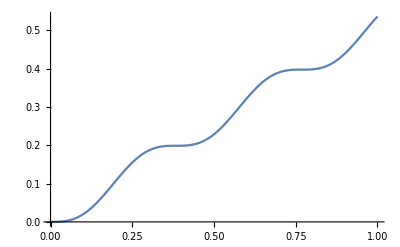

```mathematica
Plot[D[LC[t],sx]Z[t]/.a->.5/.b->7/.c->6.5/.sx->.99/.sy->.101,{t,0,1}]
```

```mathematica
betax1=Integrate[D[LC[s],sx]Z[s],s]
betax2=Integrate[D[LC[t],sy]Z[t],t];
```

-(b (-π s^2 √(a+b sx-c sy)-Cos[2 π s √(a+b sx-c sy)]/(2 π √(a+b sx-c sy))))/(4 π (a+b sx-c sy)^(3/2))

```mathematica
betax1/.a->.5/.b->7/.c->6.5
```

-(7 (-π √(0.5+7 sx-6.5 sy) t^2-Cos[2 π √(0.5+7 sx-6.5 sy) t]/(2 π √(0.5+7 sx-6.5 sy))))/(4 π (0.5+7 sx-6.5 sy)^(3/2))

```mathematica
Plot[betax1/.a->.5/.b->7/.c->6.5]
```

-Graphics-